## Collagen Numerical Eigensystems Analysis

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[]}]];
Parameters=Import["./results/Parameters","Grid"]
```

| 
L: | 5.
m: | 10
N: | 2
kappa: | 1.
sigma: | 1.
Delta: | 0.25
 | 
Extension Minimum: | 0
Extension Maximum: | 20
 | 
 | 
beta: | 4.
mu: | 6.
c: | 4.58
delta: | 19.17
b: | 2.14
k: | 1.57
ev0: | 0.81
C0: | 0.55

Results of calculated Eigenvectors using GSL C++

```mathematica
TR0=Import["./logs/TR/Phi_r_0.TR","Table"];
TR1=Import["./logs/TR/Phi_r_1.TR","Table"];
TR2=Import["./logs/TR/Phi_r_2.TR","Table"];
TR3=Import["./logs/TR/Phi_r_3.TR","Table"];
TR4=Import["./logs/TR/Phi_r_4.TR","Table"];
TR5=Import["./logs/TR/Phi_r_5.TR","Table"];

Tρ0=Import["./logs/TROE/Phi_roe_0.TROE","Table"];
Tρ1=Import["./logs/TROE/Phi_roe_1.TROE","Table"];
Tρ2=Import["./logs/TROE/Phi_roe_2.TROE","Table"];
Tρ3=Import["./logs/TROE/Phi_roe_3.TROE","Table"];
Tρ4=Import["./logs/TROE/Phi_roe_4.TROE","Table"];
Tρ5=Import["./logs/TROE/Phi_roe_5.TROE","Table"];

Tλ0=Import["./logs/TLAMBDA/Phi_lambda_0.TLAMBDA","Table"];
Tλ1=Import["./logs/TLAMBDA/Phi_lambda_1.TLAMBDA","Table"];
Tλ2=Import["./logs/TLAMBDA/Phi_lambda_2.TLAMBDA","Table"];
Tλ3=Import["./logs/TLAMBDA/Phi_lambda_3.TLAMBDA","Table"];
Tλ4=Import["./logs/TLAMBDA/Phi_lambda_4.TLAMBDA","Table"];
Tλ5=Import["./logs/TLAMBDA/Phi_lambda_5.TLAMBDA","Table"];
```

Results of analytical Eigenfunctions

```mathematica
R0=Import["./logs/R_Analytical/PSI_R_0.RA","Table"];
R1=Import["./logs/R_Analytical/PSI_R_1.RA","Table"];
R2=Import["./logs/R_Analytical/PSI_R_2.RA","Table"];
R3=Import["./logs/R_Analytical/PSI_R_3.RA","Table"];
R4=Import["./logs/R_Analytical/PSI_R_4.RA","Table"];
R5=Import["./logs/R_Analytical/PSI_R_5.RA","Table"];

ρ0=Import["./logs/ROE_Analytical/PSI_ROE_0.ROEA","Table"];
ρ1=Import["./logs/ROE_Analytical/PSI_ROE_1.ROEA","Table"];
ρ2=Import["./logs/ROE_Analytical/PSI_ROE_2.ROEA","Table"];
ρ3=Import["./logs/ROE_Analytical/PSI_ROE_3.ROEA","Table"];
ρ4=Import["./logs/ROE_Analytical/PSI_ROE_4.ROEA","Table"];
ρ5=Import["./logs/ROE_Analytical/PSI_ROE_5.ROEA","Table"];

λ0=Import["./logs/LAMBDA_Analytical/PSI_LAMBDA_0.LAMBDAA","Table"];
λ1=Import["./logs/LAMBDA_Analytical/PSI_LAMBDA_1.LAMBDAA","Table"];
λ2=Import["./logs/LAMBDA_Analytical/PSI_LAMBDA_2.LAMBDAA","Table"];
λ3=Import["./logs/LAMBDA_Analytical/PSI_LAMBDA_3.LAMBDAA","Table"];
λ4=Import["./logs/LAMBDA_Analytical/PSI_LAMBDA_4.LAMBDAA","Table"];
λ5=Import["./logs/LAMBDA_Analytical/PSI_LAMBDA_5.LAMBDAA","Table"];
```

Numerical Eigenfunction Plots

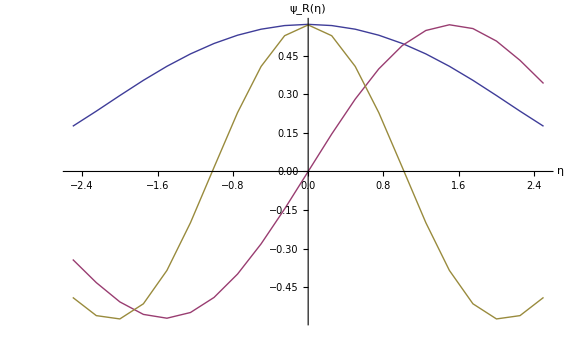

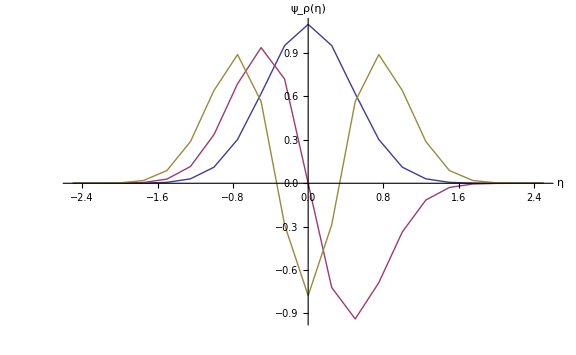

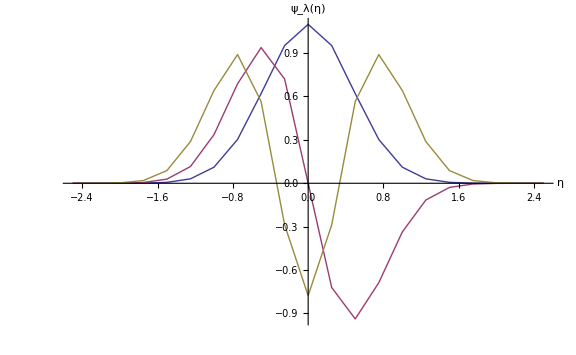

```mathematica
ListLinePlot[{TR0,TR1,TR2},ImageSize->Large,PlotRange->All,AxesLabel->{Style["η",FontSize->18],Style["ψ_R(η)",FontSize->18]}]
ListLinePlot[{Tρ0,Tρ1,Tρ2},ImageSize->Large,PlotRange->All,AxesLabel->{Style["η",FontSize->18],Style["ψ_ρ(η)",FontSize->18]}]
ListLinePlot[{Tλ0,Tλ1,Tλ2},ImageSize->Large,PlotRange->All,AxesLabel->{Style["η",FontSize->18],Style["ψ_λ(η)",FontSize->18]}]
```

Analytical Eigenfunction Plots

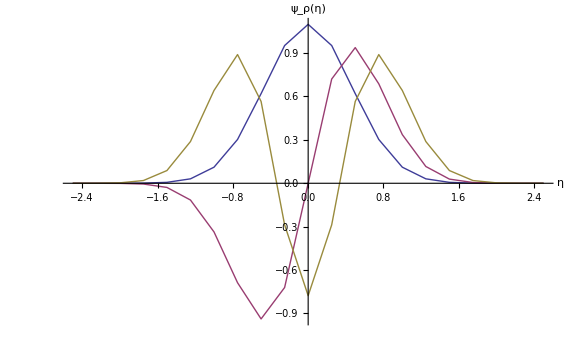

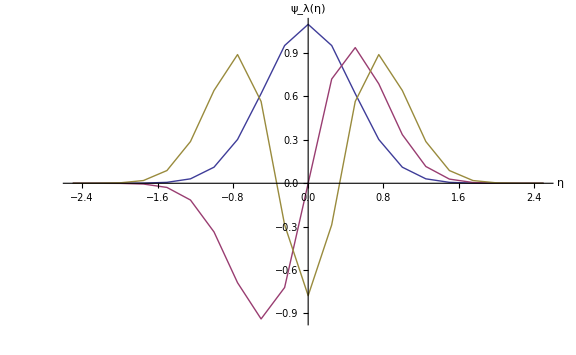

```mathematica
(*ListLinePlot[{R0,R1,R2},ImageSize->Large,AxesLabel->{Style["η",FontSize->18],Style["ψ_R(η)",FontSize->18]}]*)
ListLinePlot[{ρ0,ρ1,ρ2},ImageSize->Large,PlotRange->All,AxesLabel->{Style["η",FontSize->18],Style["ψ_ρ(η)",FontSize->18]}]
ListLinePlot[{λ0,λ1,λ2},ImageSize->Large,PlotRange->All,AxesLabel->{Style["η",FontSize->18],Style["ψ_λ(η)",FontSize->18]}]
```

Analytical Eigenfunction vs Numerical Eigenfunction Plots

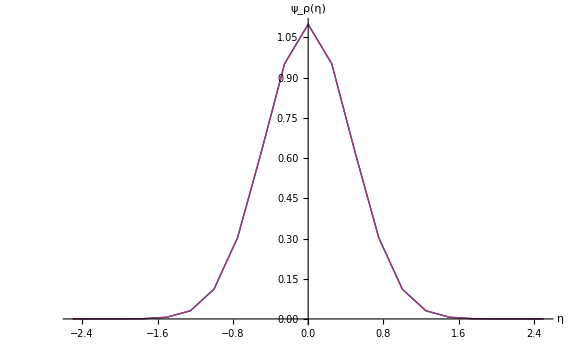

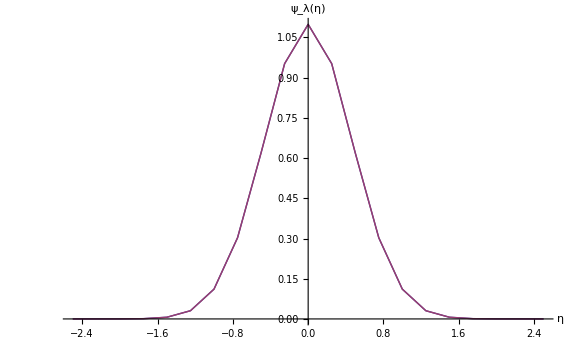

```mathematica
ListLinePlot[{ρ0,Tρ0},ImageSize->Large,PlotRange->All,AxesLabel->{Style["η",FontSize->18],Style["ψ_ρ(η)",FontSize->18]}]
ListLinePlot[{λ0,Tλ0},ImageSize->Large,PlotRange->All,AxesLabel->{Style["η",FontSize->18],Style["ψ_λ(η)",FontSize->18]}]
```

Created by: Hemant Tailor

Project Supervisor: Prof Ian Ford

text

University College London   |   Dept of Physics and Astronomy   |   London Centre of Nanotechnology